# Andre Lukas MM PS 1 - Q1

Defining the weight function and the scalar product.

```mathematica
weight[x_] := 1
scalarProduct[f_, g_] := Integrate[(f * g * weight[x]), {x, -1, 1}]
```

Defining Gram-Schmidt procedure. Takes input list of functions and forms them into an orthonormal basis relative to the above.

```mathematica
basis = {};
n = 7; (*Maximal order of basis*)
fs= Table[x^i, {i, 0, n}];  (*List of functions to turn into orthonormal basis*)

(*Gram-Schmidt process for remaining basis vectors*)
For[i = 1, i <= Length[fs], i++, (*Iterating over each function*)
For[j = 1, j <= Length[basis], j++,
fs[[i]] = fs[[i]] - scalarProduct[fs[[i]], basis[[j]]]*basis[[j]]];(*Subtracting relevant projections from each function*)
   AppendTo[basis, fs[[i]] / Sqrt[scalarProduct[fs[[i]], fs[[i]]]]];
]

basis
prop = Table[LegendreP[n, x] / Sqrt[scalarProduct[LegendreP[n, x], LegendreP[n, x]]], {n, 0, 7}];

Table[prop[[n]] - basis[[n]], {n, 0, 5}]; //Simplify
```

{1/(√2),√(3/2) x,3/2 √(5/2) (-1/3+x^2),5/2 √(7/2) (-(3 x)/5+x^3),(105 (-1/5+x^4-6/7 (-1/3+x^2)))/(8 √2),63/8 √(11/2) (-(3 x)/7+x^5-10/9 (-(3 x)/5+x^3)),231/16 √(13/2) (-1/7+x^6-5/7 (-1/3+x^2)-15/11 (-1/5+x^4-6/7 (-1/3+x^2))),429/16 √(15/2) (-x/3+x^7-35/33 (-(3 x)/5+x^3)-21/13 (-(3 x)/7+x^5-10/9 (-(3 x)/5+x^3)))}

Can now consider the projection of some more general function onto this basis, and using the result as an approximation.

```mathematica
f[x_] = Sin[x];(*Defining a general function*)
approxF = {}; (*ith element refers to f approximated with i basis polynomials, that being to (i-1)th order*)
current = 0;

For[i = 1, i <= Length[basis], i++,
current += scalarProduct[f[x], basis[[i]]]*basis[[i]];
AppendTo[approxF, current]]
```

To plot all of the approximations together.

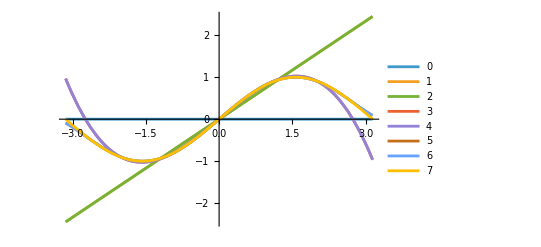

```mathematica
labels = Table[ToString[i], {i, 0, n}];
Plot[approxF, {x, -Pi, Pi}, PlotLegends->labels]
```

To plot the highest order approximation against the given function.

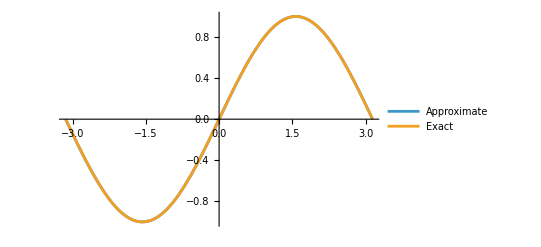

```mathematica
Plot[{approxF[[-1]], f[x]}, {x, -Pi, Pi}, PlotLegends->{"Approximate", "Exact"}]
```